Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{A→-(Kap^-α Ls^α w)/(-1+α)}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{A→0.17423}}

A→0.17423

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{w→103.408/Ls^0.3}

Line[{{150,22.55},{150,24}}]

Line[{{140,23},{150,23},{150,22.55}}]

Line[{{155,22.55},{155,24}}]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{w→22.7749}

Line[{{140,22.7749},{155,22.7749},{155,22.55}}]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{w→103.922/Ls^0.3}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{w→22.8881}

Line[{{140,22.8881},{155,22.8881},{155,22.55}}]

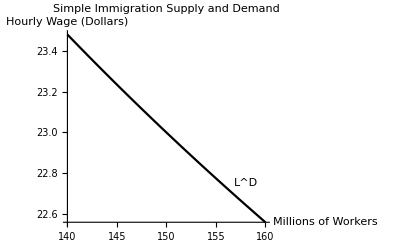

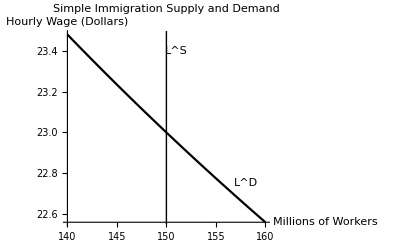

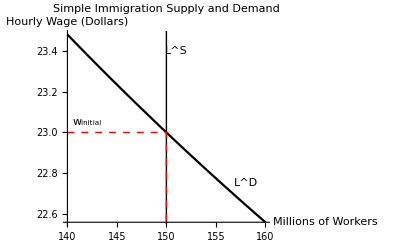

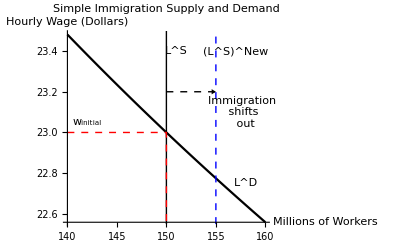

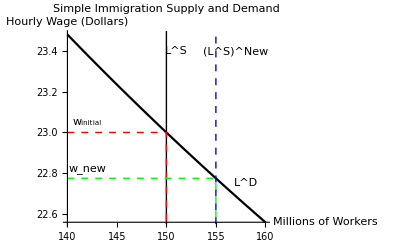

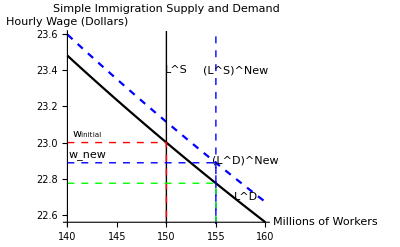

~/Dropbox/Macro_Public/Immigration/SimpleImmigration1.png

~/Dropbox/Macro_Public/Immigration/SimpleImmigration2.png

~/Dropbox/Macro_Public/Immigration/SimpleImmigration3.png

~/Dropbox/Macro_Public/Immigration/SimpleImmigration4.png

~/Dropbox/Macro_Public/Immigration/SimpleImmigration5.png

~/Dropbox/Macro_Public/Immigration/SimpleImmigration6.png

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{A→10.802}}

```mathematica
ClearAll["Global'*"]
Clear[A]
Solve[((((1-α)*A*Kap^α)/w)^(1/α)==Ls),A]
temp=Solve[((((1-α)*A*Kap^α)/w)^(1/α)==Ls*1300)/.{Ls->150000000/1000000,α->0.3,Kap->50000*150000000,w->23}]
Arule=A->(A/.temp[[1]])
temp=Solve[((((1-α)*A*Kap^α)/w)^(1/α)/.{Arule,Kap->50000*150000000,α->0.3})==Ls*1300,w][[1]]
lineStyle={Thick,Red,Dashed};
line1=Line[{{150,22.55},{150,24}}]
line2=Line[{{140,23},{150,23},{150,22.55}}]
line3=Line[{{155,22.55},{155,24}}]
temp2=Solve[((((1-α)*A*Kap^α)/w)^(1/α)/.{Arule,Kap->50000*150000000,α->0.3})==155*1300][[1]]
line4=Line[{{140,(w/.temp2)},{155,(w/.temp2)},{155,22.55}}]
temp3=Solve[((((1-α)*A*Kap^α)/w)^(1/α)/.{Arule,Kap->(50000*150000000+25000*5000000),α->0.3})==Ls*1300,w][[1]]
temp4=Solve[((((1-α)*A*Kap^α)/w)^(1/α)/.{Arule,Kap->(50000*150000000+25000*5000000),α->0.3})==155*1300,w][[1]]
line5=Line[{{140,(w/.temp4)},{155,(w/.temp4)},{155,22.55}}]
p1=Plot[{w/.{temp}},{Ls,140,160},PlotStyle->Black,PlotLabel->"Simple Immigration Supply and Demand",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},Epilog->{Text["L^D",{158,22.75}]}]
p2=Plot[{w/.{temp}},{Ls,140,160},PlotStyle->{Black},PlotLabel->"Simple Immigration Supply and Demand",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},Epilog->{Directive[{Black}],line1,Text["L^D",{158,22.75}],Text["L^S",{151,23.4}]}]
p3=Plot[{w/.{temp}},{Ls,140,160},PlotStyle->{Black},PlotLabel->"Simple Immigration Supply and Demand",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},Epilog->{Directive[{Black}],line1,Directive[{Red,Dashed}],line2,Directive[Black],Text["L^D",{158,22.75}],Text["L^S",{151,23.4}],Text["w_initial",{142,23.05}]}]
p4=Plot[{w/.{temp}},{Ls,140,160},PlotStyle->{Black},PlotLabel->"Simple Immigration Supply and Demand",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},Epilog->{Directive[{Black}],line1,Directive[{Red,Dashed}],line2,Directive[Black],Directive[{Blue}],line3,Directive[Black],Text["L^D",{158,22.75}],Text["L^S",{151,23.4}],Text["w_initial",{142,23.05}],Text[Style["Immigration \n shifts \n out",TextAlignment->Left],{157.8,23.1}],Arrow[{{150,23.2},{155,23.2}}],Text["(L^S)^New",{157,23.4}]}]
p5=Plot[{w/.{temp}},{Ls,140,160},PlotStyle->{Black},PlotLabel->"Simple Immigration Supply and Demand",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},Epilog->{Directive[{Black}],line1,Directive[{Red,Dashed}],line2,Directive[{Blue}],line3,Directive[{Green,Dashed}],line4,Directive[Black],Text["L^D",{158,22.75}],Text["L^S",{151,23.4}],Text["w_initial",{142,23.05}],Text["(L^S)^New",{157,23.4}],Text["w_new",{142,22.77+0.05}]}]
p6=Plot[{w/.{temp},w/.{temp3}},{Ls,140,160},PlotStyle->{Black,{Dashed,Blue}},PlotLabel->"Simple Immigration Supply and Demand",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},Epilog->{Directive[{Black}],line1,Directive[{Red,Dashed}],line2,Directive[{Blue}],line3,Directive[{Green,Dashed}],line4,Directive[Blue,Dashed],line5,Directive[Black],Text["L^D",{158,22.7}],Directive[Black],Text["(L^D)^New",{158,22.9}],Text["L^S",{151,23.4}],Text["w_initial",{142,23.05}],Text["(L^S)^New",{157,23.4}],Text["w_new",{142,22.88+0.05}]}]
Export["~/Dropbox/Macro_Public/Immigration/SimpleImmigration1.png",p1,ImageResolution->300]
Export["~/Dropbox/Macro_Public/Immigration/SimpleImmigration2.png",p2,ImageResolution->300]
Export["~/Dropbox/Macro_Public/Immigration/SimpleImmigration3.png",p3,ImageResolution->300]
Export["~/Dropbox/Macro_Public/Immigration/SimpleImmigration4.png",p4,ImageResolution->300]
Export["~/Dropbox/Macro_Public/Immigration/SimpleImmigration5.png",p5,ImageResolution->300]
Export["~/Dropbox/Macro_Public/Immigration/SimpleImmigration6.png",p6,ImageResolution->300]
```

```mathematica
Simplify[D[ϕ*(al*Ll^((σ-1)/σ)+ah*Lh^((σ-1)/σ))^(σ/(σ-1))-wl*Ll,Ll]]
TeXForm[Simplify[D[D[ϕ*(al*Ll^((σ-1)/σ)+ah*Lh^((σ-1)/σ))^(σ/(σ-1)),Ll],Lh]]]
```

7.80495 Ll^(-1/σ) (0.802387 Lh^((-1+σ)/σ)+0.197613 Ll^((-1+σ)/σ))^(1/(-1+σ))-wl

\frac{160.371 \text{Lh}^{\frac{1}{\sigma }} \text{Ll}^{\frac{1}{\sigma }} \left(0.802387 \text{Lh}^{\frac{\sigma -1}{\sigma }}+0.197613 \text{Ll}^{\frac{\sigma -1}{\sigma
   }}\right)^{\frac{\sigma }{\sigma -1}}}{\sigma  \left(1. \text{Ll} \text{Lh}^{\frac{1}{\sigma }}+4.0604 \text{Lh} \text{Ll}^{\frac{1}{\sigma }}\right)^2}

```mathematica
Clear[σ,Lh,Ll,ah,al,ϕ]
D[ϕ*(al*Ll^((σ-1)/σ)+ah*Lh^((σ-1)/σ))^(σ/(σ-1)),Lh]
Clear[al]
σ->1.5
temp=Solve[({(1-al) Lh^(-1+(-1+σ)/σ) ((1-al) Lh^((-1+σ)/σ)+al Ll^((-1+σ)/σ))^(-1+σ/(-1+σ)) ϕ==29.16,
al/(1-al)*(Lh/Ll)^(1/σ)==11.4/29.16}/.{σ->1.5,Lh->100,Ll->50}),{al,ϕ}]
al={al/.temp}[[1,1]];
ah=1-al;
ϕ={ϕ/.temp}[[1,1]];
```

ah Lh^(-1+(-1+σ)/σ) (ah Lh^((-1+σ)/σ)+al Ll^((-1+σ)/σ))^(-1+σ/(-1+σ)) ϕ

σ→1.5

{{al→0.197613,ϕ→39.4962}}

wl→7.80495 Llx^(-1.+(-1.+σ)/σ) (0.802387 Lh^((-1+σ)/σ)+0.197613 Llx^((-1+σ)/σ))^(-1.+σ/(-1.+σ))

wh→31.6913 Lhx^(-1.+(-1.+σ)/σ) (0.802387 Lhx^((-1+σ)/σ)+0.197613 Ll^((-1+σ)/σ))^(-1.+σ/(-1.+σ))

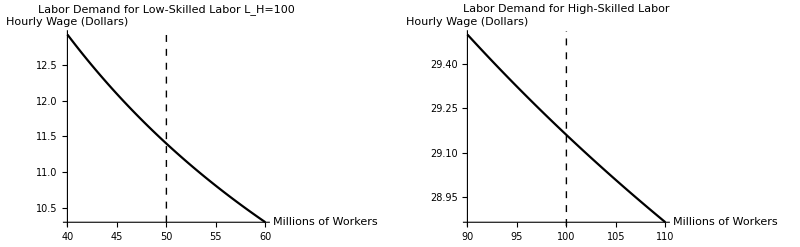

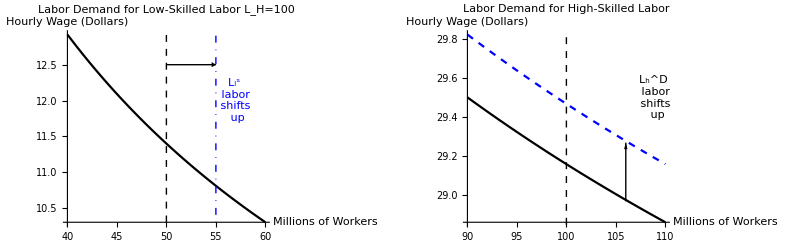

~/Dropbox/Macro_Public/Immigration/HetImmigration1.png

~/Dropbox/Macro_Public/Immigration/HetImmigration2.png

```mathematica
LlD1=Solve[(D[ϕ*(al*Ll^((σ-1)/σ)+ah*Lh^((σ-1)/σ))^(σ/(σ-1))-wl*Ll-wh*Lh,Ll]==0/.{Ll->Llx}),wl][[1,1]]
LhD1=Solve[(D[ϕ*(al*Ll^((σ-1)/σ)+ah*Lh^((σ-1)/σ))^(σ/(σ-1))-wl*Ll-wh*Lh,Lh]==0/.{Lh->Lhx}),wh][[1,1]]

p0a=Plot[(wl/.LlD1)/.{Lh->100,σ->1.5},{Llx,40,60},PlotLabel->"Labor Demand for Low-Skilled Labor \n L_H=100",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},PlotStyle->Black,Epilog->{Directive[Black,Dashed],Line[{{50,10.3},{50,13.5}}]}];
p0b=Plot[(wh/.LhD1)/.{Ll->50,σ->1.5},{Lhx,90,110},PlotLabel->"Labor Demand for High-Skilled Labor",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},PlotStyle->Black,Epilog->{Directive[Black,Dashed],Line[{{100,28.85},{100,29.9}}]}];
g0=GraphicsGrid[{{p0a,p0b}},Spacings->0]
p1a=Plot[(wl/.LlD1)/.{Lh->100,σ->1.5},{Llx,40,60},PlotLabel->"Labor Demand for Low-Skilled Labor \n L_H=100",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},PlotStyle->Black,Epilog->{Arrow[{{50,12.5},{55,12.5}}],Directive[Black,Dashed],Line[{{50,10.3},{50,13.5}}],Directive[Blue,DotDashed],Line[{{55,10.3},{55,13.5}}],Text["L_l^s \n labor \n shifts \n up",{57,12}]}];
p1b=Plot[{(wh/.LhD1)/.{Ll->50,σ->1.5},(wh/.LhD1)/.{Ll->55,σ->1.5}},{Lhx,90,110},PlotLabel->"Labor Demand for High-Skilled Labor",AxesLabel->{"Millions \n of Workers","Hourly Wage (Dollars)"},PlotStyle->{Black,{Blue,Dashed}},Epilog->{Arrow[{{106,28.97},{106,29.27}}],Directive[Black,Dashed],Line[{{100,28.85},{100,29.9}}],Text["L_h^D \n labor \n shifts \n up",{109,29.5}]}];
g1=GraphicsGrid[{{p1a,p1b}},Spacings->0]
Export["~/Dropbox/Macro_Public/Immigration/HetImmigration1.png",g0,ImageResolution->300]
Export["~/Dropbox/Macro_Public/Immigration/HetImmigration2.png",g1,ImageResolution->300]
```

```mathematica
temp=Solve[({(1-al) Lh^(-1+(-1+σ)/σ) ((1-al) Lh^((-1+σ)/σ)+al Ll^((-1+σ)/σ))^(-1+σ/(-1+σ)) ϕ==wh,
al/(1-al)*(Lh/Ll)^(1/σ)==wl/wh}/.{σ->1.5,Lh->100,Ll->50,al->0.197613,ϕ->39.4962}),{wh,wl}]
temp=Solve[({(1-al) Lh^(-1+(-1+σ)/σ) ((1-al) Lh^((-1+σ)/σ)+al Ll^((-1+σ)/σ))^(-1+σ/(-1+σ)) ϕ==wh,
al/(1-al)*(Lh/Ll)^(1/σ)==wl/wh}/.{σ->1.5,Lh->100,Ll->55,al->0.197613,ϕ->39.4962}),{wh,wl}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{wh→29.16,wl→11.4}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{wh→29.4687,wl→10.8114}}

```mathematica
{(10.8114135858826/29.4687-11.4/29.16)/(11.4/29.16)}
```

{-0.0615651}

```mathematica
(55/100-50/100)/(50/100)//N
1/1.5*(55/100-50/100)/(50/100)//N
```

0.1

0.0666667

```mathematica
temp=Solve[({(1-al) Lh^(-1+(-1+σ)/σ) ((1-al) Lh^((-1+σ)/σ)+al Ll^((-1+σ)/σ))^(-1+σ/(-1+σ)) ϕ==wh,
al/(1-al)*(Lh/Ll)^(1/σ)==wl/wh}/.{σ->10,Lh->100,Ll->50,al->0.197613,ϕ->39.4962}),{wh,wl}]
temp=Solve[({(1-al) Lh^(-1+(-1+σ)/σ) ((1-al) Lh^((-1+σ)/σ)+al Ll^((-1+σ)/σ))^(-1+σ/(-1+σ)) ϕ==wh,
al/(1-al)*(Lh/Ll)^(1/σ)==wl/wh}/.{σ->10,Lh->100,Ll->55,al->0.197613,ϕ->39.4962}),{wh,wl}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{wh→31.3543,wl→8.27621}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{wh→31.3906,wl→8.20717}}

```mathematica
(31.390554251500646/31.354341973621974-1)
```

0.00115494

```mathematica
29.47/29.16
```

1.01063

```mathematica
ClearAll["Global'*"]
```

486.653

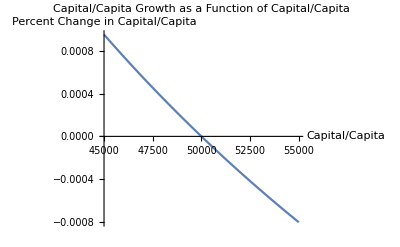

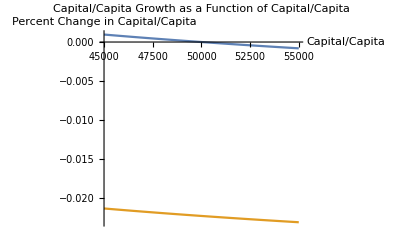

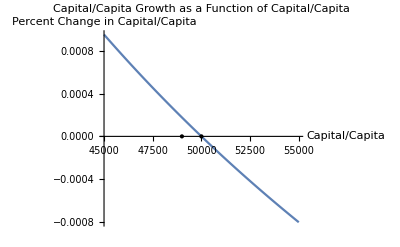

~/Dropbox/Macro_Public/Immigration/Solow1.png

~/Dropbox/Macro_Public/Immigration/Solow2.png

~/Dropbox/Macro_Public/Immigration/Solow3.png

486.653

{0.01,0.01,0.01,0.01,0.01,0.01,0.032258,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01}

{50000}

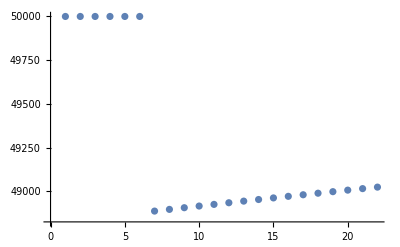

Part::partd: Part specification A⟦1⟧ is longer than depth of object.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

Hold[A⟦1⟧]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

-Graphics-

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

-Graphics-

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

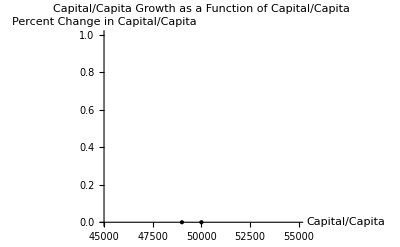

~/Dropbox/Macro_Public/Immigration/Solow1.png

~/Dropbox/Macro_Public/Immigration/Solow2.png

~/Dropbox/Macro_Public/Immigration/Solow3.png

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

Hold[A=(A/.Solve[s A k^(α-1)==s δ+n/.{s→0.05,k→50000,δ→0.05,n→0.01,α→0.3}])⟦1⟧]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

-Graphics-

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

-Graphics-

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

-Graphics-

~/Dropbox/Macro_Public/Immigration/Solow1.png

~/Dropbox/Macro_Public/Immigration/Solow2.png

~/Dropbox/Macro_Public/Immigration/Solow3.png

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

Hold[A=(A/.Solve[s A k^(α-1)==s δ+n/.{s→0.05,k→50000,δ→0.05,n→0.01,α→0.3}])⟦1⟧]

{0.01,0.01,0.01,0.01,0.01,0.01,0.032258,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01}

{50000}

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

Part::partw: Part 2 of {50000} does not exist.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

Part::partw: Part 3 of {50000} does not exist.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A⟦1⟧.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part 4 of {50000} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

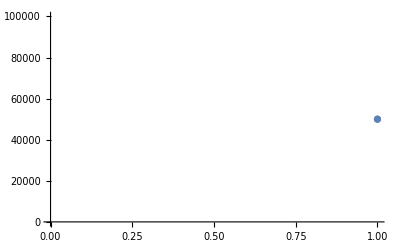

```mathematica
Clear[A,n]
A=(A/.Solve[(s*A*k^(α-1)==(s*δ+n))/.{s->0.05,k->50000,δ->0.05,n->0.01,α->0.3}])[[1]]
g1=Plot[({s*A*k^(α-1)-(s*δ+n)}/.{s->0.05,δ->0.05,n->0.01,α->0.3}),{k,45000,55000},PlotLabel->"Capital/Capita Growth as a Function of Capital/Capita",AxesLabel->{"Capital/Capita","Percent Change in Capital/Capita"}]
g2=Plot[({s*A*k^(α-1)-(s*δ+n)/.{s->0.05,δ->0.05,n->0.01,α->0.3},s*A*k^(α-1)-(s*δ+n)/.{s->0.05,δ->0.05,n->0.032258,α->0.3}}),{k,45000,55000},PlotLabel->"Capital/Capita Growth as a Function of Capital/Capita",AxesLabel->{"Capital/Capita","Percent Change in Capital/Capita"}]
g3=Plot[{s*A*k^(α-1)-(s*δ+n)/.{s->0.05,δ->0.05,n->0.01,α->0.3}},{k,45000,55000},Epilog->{PointSize[Large],Point[{50000,0}],Point[{50000*(0.98),0}]},PlotLabel->"Capital/Capita Growth as a Function of Capital/Capita",AxesLabel->{"Capital/Capita","Percent Change in Capital/Capita"}]
Export["~/Dropbox/Macro_Public/Immigration/Solow1.png",g1,ImageResolution->300]
Export["~/Dropbox/Macro_Public/Immigration/Solow2.png",g2,ImageResolution->300]
Export["~/Dropbox/Macro_Public/Immigration/Solow3.png",g3,ImageResolution->300]
ClearAll["Global'*"]
A=(A/.Solve[(s*A*k^(α-1)==(s*δ+n))/.{s->0.05,k->50000,δ->0.05,n->0.01,α->0.3}])[[1]]
nlist={0.01,0.01,0.01,0.01,0.01,0.01,0.032258,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01}
klist={50000}
Do[klist=Flatten[{klist,klist[[t-1]]*(1+(s*A*klist[[t-1]]^(α-1)-(s*δ+nlist[[t]])))/.{s->0.05,k->50000,δ->0.05,n->0.01,α->0.3}}],{t,2,Length[nlist]}]
ListPlot[klist]
```

```mathematica
klist
```

```mathematica
t=2
```

2

{{50000},50000.}

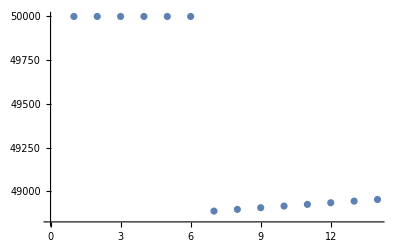

{{A→486.653}}

{24.3326/k^0.7,0.0125}

```mathematica
{klist,}
```

```mathematica
(50000*150000000)/155000000//N
```

48387.1

```mathematica
48387.1/50000-1
```

-0.032258